0.618034

gamma =  0.99

eq1 : -20.6175

eq2 : 34.9183

eq3 : 52.3321

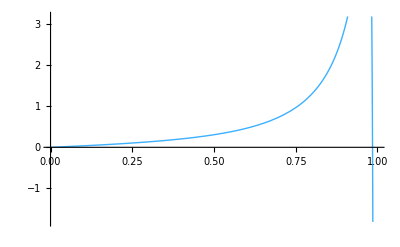

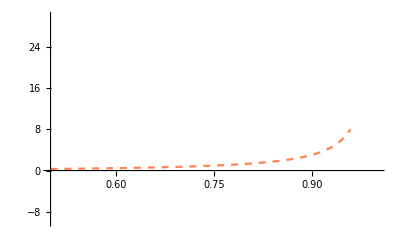

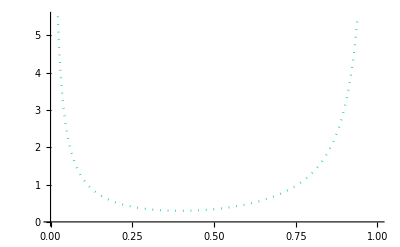

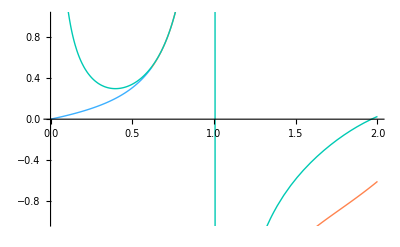

```mathematica
Clear[γ]
eq = (γ (40+70 γ-25 γ^2-61 γ^3+20 γ^4+10 γ^5-40 γ^6-20 γ^7))/(120 (-1+γ)^2 (1+γ)^3);
eq2 = -(-1+5 γ+39 γ^2+45 γ^3+39 γ^4+35 γ^5+19 γ^6-5 γ^7-6 γ^8)/(120 (-1+γ) γ (1+γ)^2);
eq3 = (15+5 γ-80 γ^2+80 γ^3+265 γ^4-88 γ^5-285 γ^6+95 γ^8+5 γ^9-10 γ^10)/(120 (-1+γ)^2 γ (1+γ)^3);

x = (Sqrt[5]-1)/2 //N
γ=0.99;
factor = (1-γ)/γ;
factor = 1;
Print["gamma =  ",γ];
Print["eq1 : ", eq*factor //Simplify //N];
Print["eq2 : ", eq2*factor //Simplify //N];
Print["eq3 : ", eq3*factor //Simplify //N];
(*
Show[Plot[eq*factor,{γ,0.9,1},PlotStyle->{{Thick,ColorData[96][1]}}], 
PlotRange->{{0,1},{0,6}}]
*)
Show[Plot[eq*factor,{γ,0,1},PlotStyle->{{Thick,ColorData[96][1]}}]]

Show[
Plot[eq2*factor,{γ,.5,1},PlotStyle->{{Dashed,ColorData[96][2]}}],
PlotRange->{{.5,1},{-10,30}}]

Show[Plot[eq3*factor,{γ,0,1},PlotStyle->{{Dotted,ColorData[96][3]}}]]
Show[Plot[eq*factor,{γ,0,x},PlotStyle->{{Thick,ColorData[96][1]}}], 
Plot[eq2*factor,{γ,x,2},PlotStyle->{{Thick,ColorData[96][2]}}],
Plot[eq3*factor,{γ,0,2},PlotStyle->{{Thick,ColorData[96][3]}}],
PlotRange->{{0,2},{-1,1}}]
```